# Distribution decomposition by runs

## Initialization and options

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory[NotebookDirectory[]],"EconomicComputations.wl"}]];
```

```mathematica
Middle[l_List]:=Part[l,Floor[Length[l]/2]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};

(* Opciones de los procedimientos *)
windowsize = 252;
resolution = 40;
symmetryPoints = 50;
```

### Package information

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Load database

```mathematica
database = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Datasets","DJI_DAX_MXX_NIKKEI_dataset.mx"}]];
AddToDataset[database,"TrendReturns",TrendReturns,{"Prices"}];
AddToDataset[database,"DatedTrendReturns",DatedTrendReturns,{"Dates","Prices"}];
AddToDataset[database,"VelocityTrendReturns",VelocityTrendReturns,{"Prices"}];
AddToDataset[database,"DatedVelocityTrendReturns",DatedVelocityTrendReturns,{"Dates","Prices"}];
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Crisis interval

Add database information

```mathematica
rules = {"Japanese asset\nprice bubble"-> "(a)","Tequila effect"->"(b)","Dotcom bubble"->"(c)","Subprime crisis"->"(d)","Brexit"->"(e)"};
dateNames = {"Japanese asset\nprice bubble","Tequila effect","Dotcom bubble","Subprime crisis","Brexit"}/.rules;
dateObjects = {DateObject[{1990,1,1},"Day","Gregorian",-5.],DateObject[{1994,1,1},"Day","Gregorian",-5.],DateObject[{2000,3,10},"Day","Gregorian",-5.],DateObject[{2007,8,9},"Day","Gregorian",-5.],DateObject[{2016,6,23},"Day","Gregorian",-5.]};

AddKeyToMarket[database[[1]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[1]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[2]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[2]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[3]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[3]],"ImportantDates"->dateObjects];

AddKeyToMarket[database[[4]],"ImportantDatesNames"->dateNames];
AddKeyToMarket[database[[4]],"ImportantDates"->dateObjects];

orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

## Returns distribution

```mathematica
MakeStatisticTable[marketnames_,dists_] := Module[{gridmm},
gridmm = {Join[{""},marketnames],
Join[{"μ"},Table[Mean[i],{i,dists}]],
Join[{"σ"}, Table[StandardDeviation[i],{i,dists}]],
Join[{"Skewness"}, Table[Skewness[i],{i,dists}]],
Join[{"Kurtosis"}, Table[Kurtosis[i],{i,dists}]]};
Grid[gridmm,
Alignment->Left,
Spacings->{2,1},
Frame->All,
ItemStyle->"Text",
Background->{{LightGray,None},{Gray,None}}
]
];
```

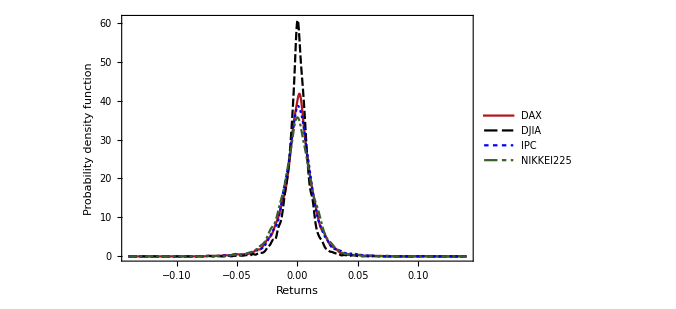

```mathematica
SmoothHistogram[database[[All,"Returns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"Returns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000319714 | 0.000296114 | 0.000555369 | -0.0000312847
σ | 0.0142415 | 0.0107171 | 0.0148833 | 0.0151916
Skewness | -0.106661 | -0.176113 | 0.0226418 | -0.203261
Kurtosis | 7.30022 | 11.569 | 9.35525 | 8.09446

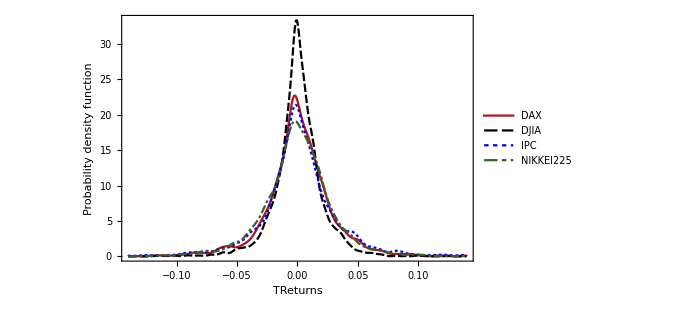

```mathematica
SmoothHistogram[database[[All,"TrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["TReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"TrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000631323 | 0.000563473 | 0.00120697 | -0.000059991
σ | 0.0295203 | 0.0208431 | 0.0342922 | 0.0300463
Skewness | -0.729049 | -0.693697 | -0.241625 | -0.569394
Kurtosis | 10.8335 | 14.9535 | 9.67833 | 11.9555

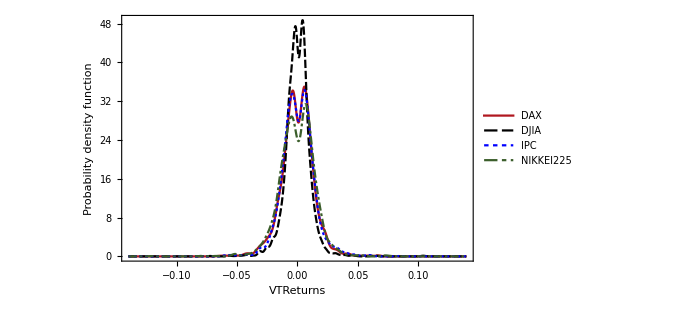

```mathematica
SmoothHistogram[database[[All,"VelocityTrendReturns"]],
PlotTheme->"Monochrome",
FrameLabel->{Style["VTReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->Placed[database[[All,"Name"]],{Right,Top}],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotRange->{{-0.14,0.14},Full}
]
```

```mathematica
MakeStatisticTable[database[[All,"Name"]],database[[All,"VelocityTrendReturns"]]]
```

| DAX | DJIA | IPC | NIKKEI225
μ | 0.000127415 | 0.000166781 | 0.00046062 | -0.0000621582
σ | 0.0131252 | 0.0103054 | 0.0131251 | 0.0142704
Skewness | -0.0275892 | 0.378788 | 0.152915 | -0.257632
Kurtosis | 5.43131 | 13.9691 | 5.84517 | 6.8131

```mathematica
hr = Map[{#["Name"],MeasureHeightRatio[#["VelocityTrendReturns"]]}&,database];
```

```mathematica
Grid[Prepend[hr,{"Name","Height ratio"}],Frame->All,Background->{None,{LightGray}}]
```

Name | Height ratio
DAX | 1.0235
DJIA | 1.02463
IPC | 1.02328
NIKKEI225 | 1.08783

## Distribution decomposition by runs

```mathematica
DayLegends[n_Integer]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
Range[n]
];

GroupReturnsByRun[market_,returnType_]:=KeySort[GroupBy[Thread[{TrendDuration[market["Prices"]],market[returnType]}],First->Last]];
PlotTrendDistributionByRuns[market_,returnType_]:=Block[{grouped},
grouped = Select[GroupReturnsByRun[market,returnType],Length[#]>40&];
SmoothHistogram[Take[grouped,4],
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style[returnType/.{"TrendReturns"->"TReturns","VelocityTrendReturns"->"TVReturns"},bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Left,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotLabel->market["Name"]
]
];
```

Trend Returns

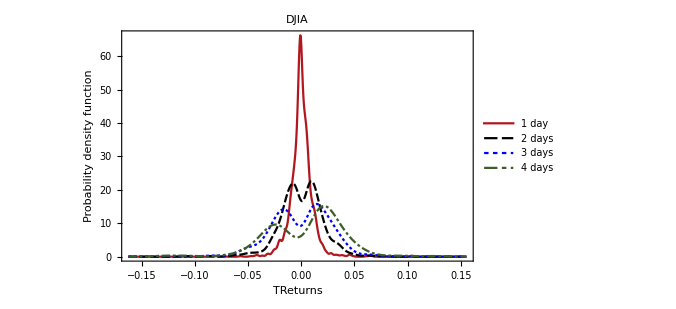
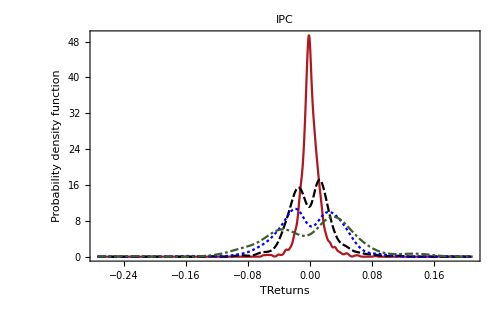
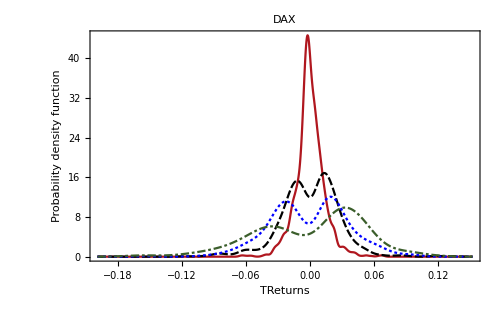
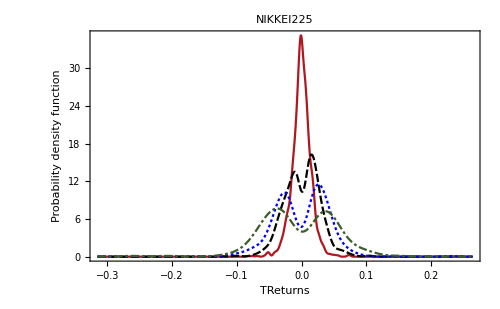

```mathematica
Map[PlotTrendDistributionByRuns[#,"TrendReturns"]&,orderedDatabase]
```

Velocity Trend Returns

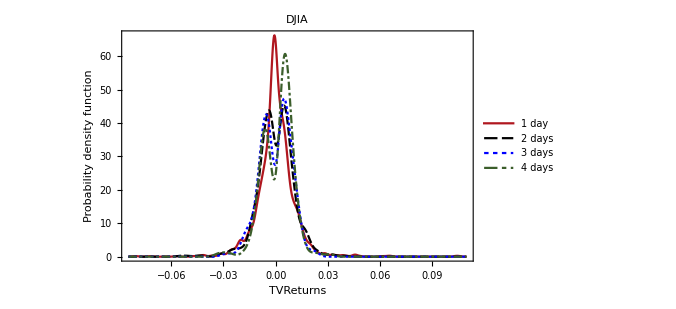
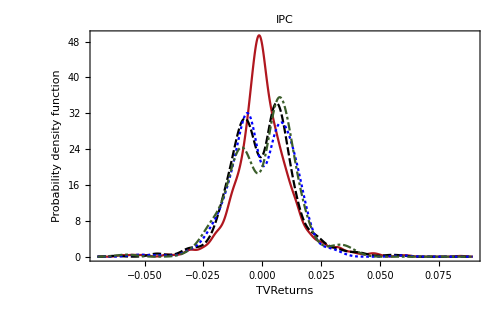
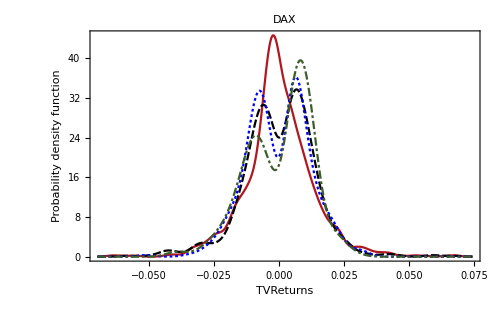
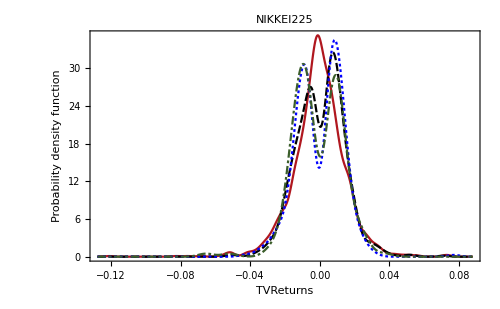

```mathematica
Map[PlotTrendDistributionByRuns[#,"VelocityTrendReturns"]&,orderedDatabase]
```

Trend decomposition symmetrycc

```mathematica
PlotSymmetryOfReturns[returns_]:= Module[{standardError,tn,upperLineLimit,meanline,cMax,cMin,cFill,cline,upp,plotData,p},
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];

cMin = Line[{{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMin"],upperLineLimit/2.5}}];
cMax = Line[{{tn["PlausibleSymmMax"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}}];
cFill = Rectangle[{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}];

cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",bigFontSize],
Style["T_n(c)",bigFontSize]
},
Epilog->{
meanline,
cline,
cMin,
cMax,

{
Gray,
Opacity[0.4],
cFill
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["C_Max"],{tn["PlausibleSymmMax"],upperLineLimit/2}],
Inset[Text["C_Min"],{tn["PlausibleSymmMin"],upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}], 
ImageSize->plotSize,Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];

PlotSymmetryOfRuns[market_]:=Block[{grouped},
grouped = Select[GroupReturnsByRun[market,"TrendReturns"],Length[#]>100&];
Labeled[Map[PlotSymmetry,grouped],market["Name"],Top]
];
```

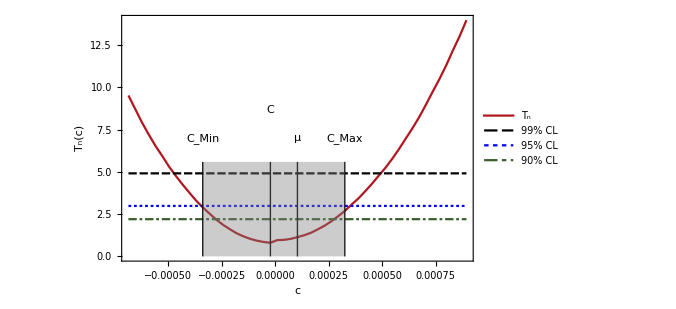
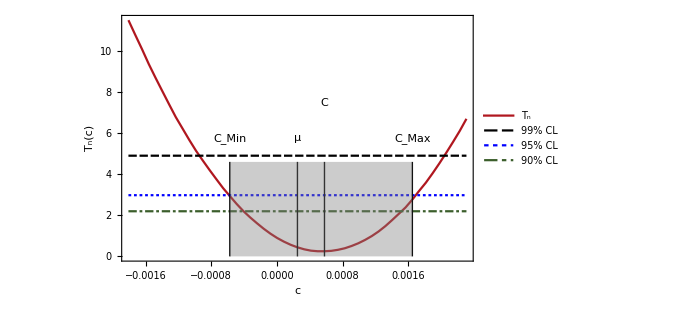
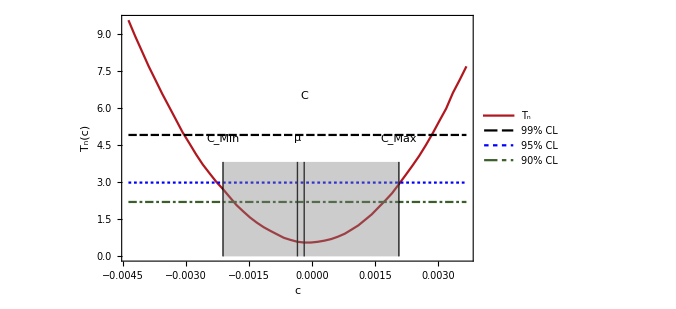
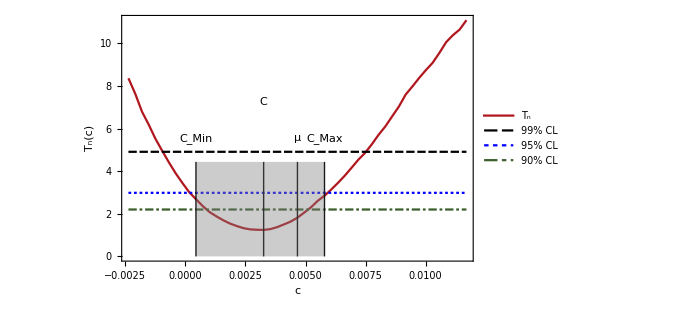
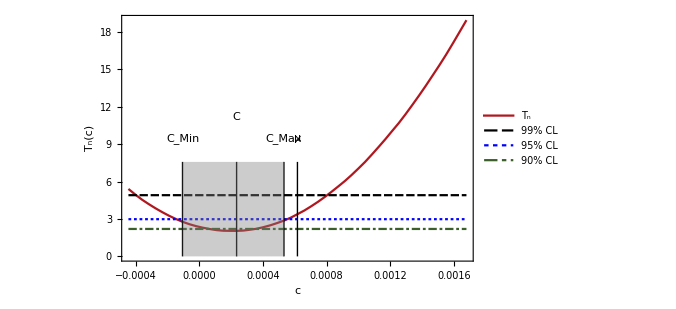
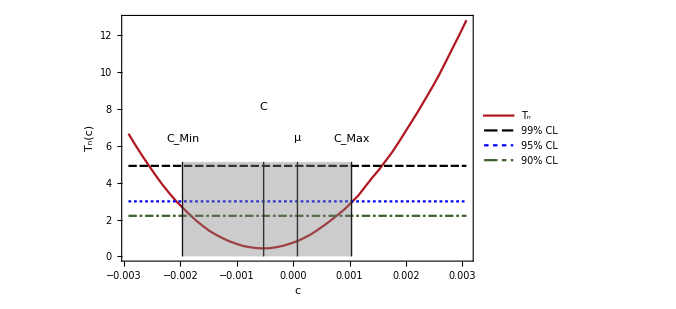
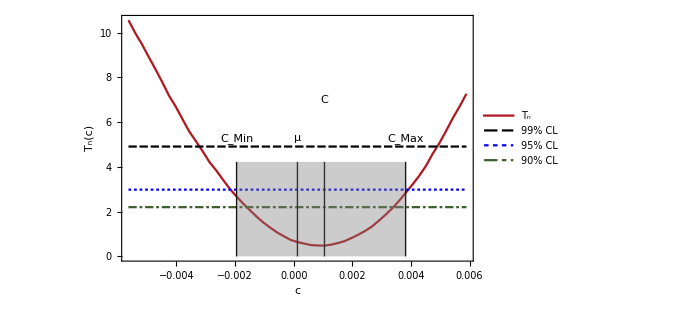
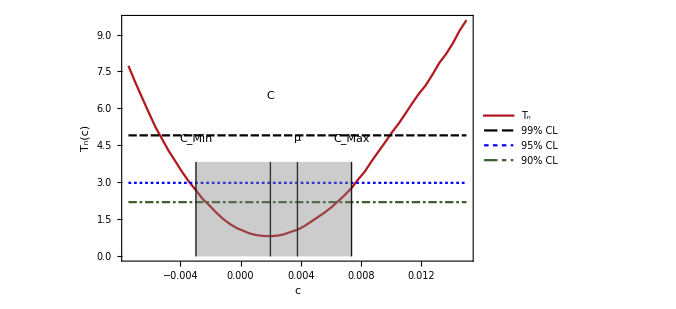
{<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>DJIA,<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-|>IPC,<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-,5→-Graphics-|>DAX,<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>NIKKEI225}

```mathematica
Map[PlotSymmetryOfRuns,orderedDatabase]
```

Trend decomposition in time

```mathematica
GroupReturnsByRun[runReturns_]:=KeyTake[KeySort[GroupBy[runReturns,First->Last]],{1,2,3,4}];
RunDistInTime[market_,windowSize_]:=DynamicModule[{runReturns,part,groupedInTime},
runReturns = Thread[{TrendDuration[market["Prices"]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,1];
groupedInTime = Map[GroupReturnsByRun,part];

Manipulate[
SmoothHistogram[
groupedInTime[[i]],
PlotRange->{{-0.06,0.06},{0,110}},
PlotTheme->"Monochrome",
FrameLabel->{Style["TReturns",bigFontSize],Style["Probability density function",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Left,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotLabel->First@market["DatedTrendReturns"][[i]]
]
,
{i,1,Length[groupedInTime],1}
]
];
```

```mathematica
orderedDatabase[[All,"Name"]]
```

{DJIA,IPC,DAX,NIKKEI225}

```mathematica
Map[RunDistInTime[#,504]&,orderedDatabase]
```

Trend decomposition time series

### Average

```mathematica
μByRun[runs_]:=Map[
{Last[#][[1]],Mean[#[[All,2]]]}&,
runs
];

RunμInTime[market_,windowSize_,runs_:{1,2,3}]:=Block[{runReturns,part,groupedInTime,symmInTime,objSize,pltData},
runReturns = Thread[{TrendDuration[market["Prices"]],market["DatedTrendReturns"][[All,1]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,1];
groupedInTime = Map[Part[GroupDatedReturnsByRun[#],runs]&,part];
symmInTime = Map[μByRun,groupedInTime];

objSize = Length[First[symmInTime]];
pltData = Table[symmInTime[[All,i]],{i,objSize}];

DateListPlot[
pltData,
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["μ",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[runs],{Left,Bottom}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotMarkers->None,
PlotLabel->market["Name"],
GridLines->{{},{0}}
]
];

RunμSignalCorrelation[market_,windowSize_,runs_:{1,2,3},skip_:1]:=Block[{runReturns,part,groupedInTime,symmInTime,objSize,pltData,onlyData,corr},
runReturns = Thread[{TrendDuration[market["Prices"]],market["DatedTrendReturns"][[All,1]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,skip];
groupedInTime = Map[Part[GroupDatedReturnsByRun[#],runs]&,part];
symmInTime = Map[μByRun,groupedInTime];

objSize = Length[First[symmInTime]];
pltData = Table[symmInTime[[All,i]],{i,objSize}];

onlyData = pltData[[All,All,2]];
corr = Table[Correlation[onlyData[[i]],onlyData[[j]]],{i,1,3},{j,1,3}];

corr
];
```

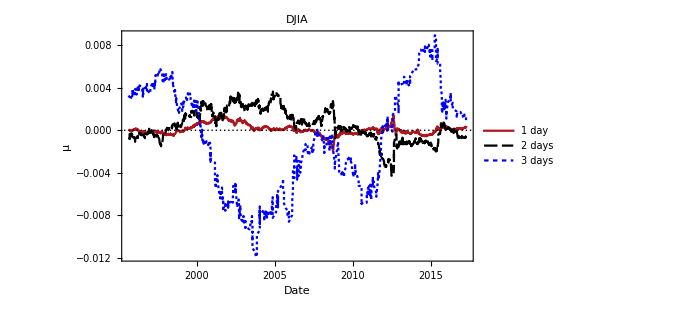
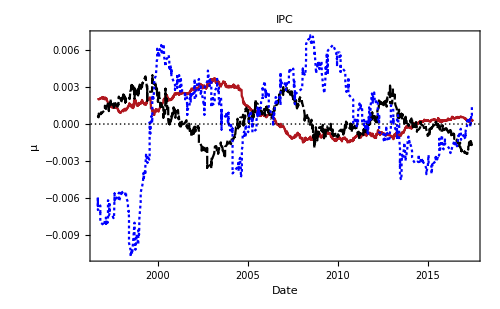
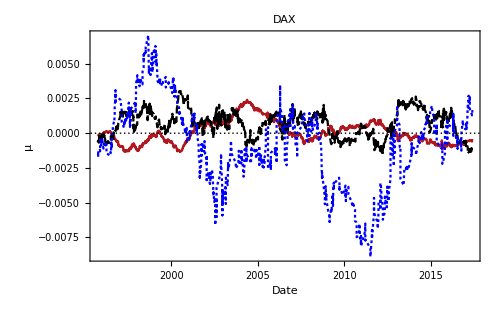
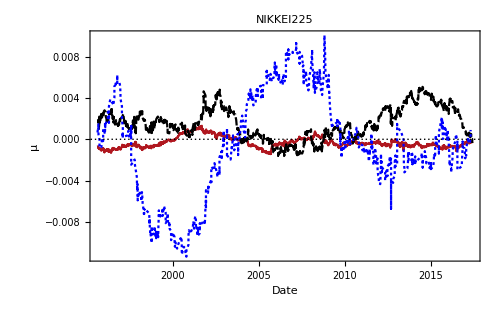

```mathematica
ProgressMap[RunμInTime[#,504]&,orderedDatabase]
```

```mathematica
correlations = ProgressMap[RunμSignalCorrelation[#,504]&,orderedDatabase];
```

```mathematica
MapThread[Labeled[MatrixForm[#1],#2,Top]&,{correlations,orderedDatabase[[All,"Name"]]}]
```

{(1. | 0.278936 | -0.388815
0.278936 | 1. | -0.633582
-0.388815 | -0.633582 | 1.)DJIA,(1. | -0.182622 | -0.224301
-0.182622 | 1. | -0.258607
-0.224301 | -0.258607 | 1.)IPC,(1. | -0.326995 | -0.515551
-0.326995 | 1. | 0.328624
-0.515551 | 0.328624 | 1.)DAX,(1. | -0.113624 | -0.32472
-0.113624 | 1. | -0.467022
-0.32472 | -0.467022 | 1.)NIKKEI225}

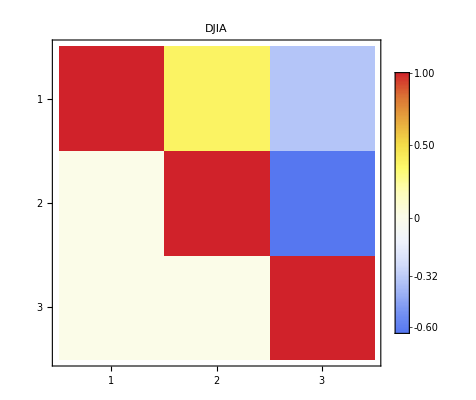
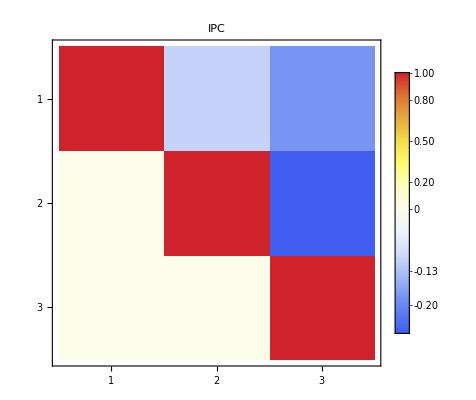
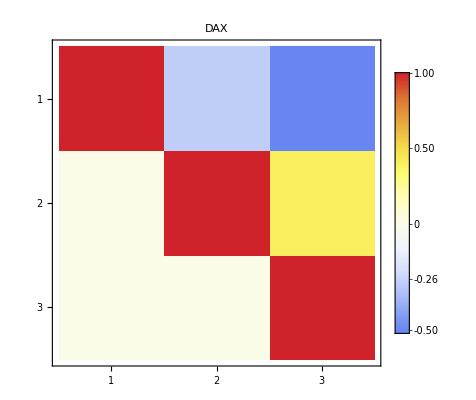
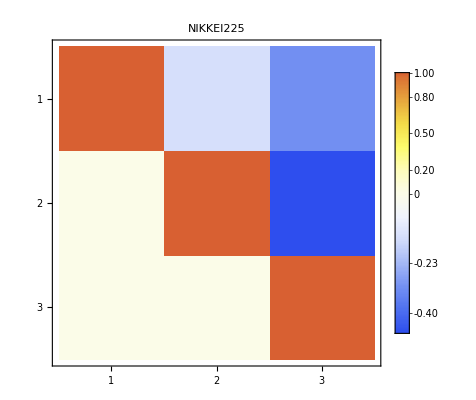

```mathematica
hideLower = UpperTriangularize[ConstantArray[1,{3,3}]];
MapThread[
MatrixPlot[
hideLower*#1,
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
PlotRange->{All,All,{-1,1}},
PlotLabel->#2,
PlotTheme->"Monochrome"
]&,
{correlations,orderedDatabase[[All,"Name"]]}
]
```

### Symmetry analysis

```mathematica
DayLegends[l_List]:=Map[
If[# == 1,
StringJoin[ToString[#]," day"],
StringJoin[ToString[#]," days"]
]
&,
l
];

ClosestDate[list_,date_]:=First[MinimalBy[list,Abs[QuantityMagnitude[DateDifference[First[#],date]]]&]];

GroupDatedReturnsByRun[runReturns_]:=KeyTake[KeySort[GroupBy[runReturns,First->Extract[{{2},{3}}]]],{1,2,3,4}];
CByRun[runs_]:=Map[
{Last[#][[1]],MeasureTn[#[[All,2]],0.05,50]["BestSymmetry"]}&,
runs
];

RunCInTime[market_,windowSize_,runs_:{1,2,3,4}]:=Block[{runReturns,part,groupedInTime,symmInTime,objSize,pltData},
runReturns = Thread[{TrendDuration[market["Prices"]],market["DatedTrendReturns"][[All,1]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,1];
groupedInTime = Map[Part[GroupDatedReturnsByRun[#],runs]&,part];
symmInTime = Map[CByRun,groupedInTime];

objSize = Length[First[symmInTime]];
pltData = Table[symmInTime[[All,i]],{i,objSize}];

DateListPlot[
pltData,
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["C",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[runs],{Left,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->colors,
PlotMarkers->None,
PlotLabel->market["Name"],
GridLines->{{},{0}}
]
];

RunCSignalCorrelation[market_,windowSize_,runs_:{1,2,3,4},skip_:1]:=Block[{runReturns,part,groupedInTime,symmInTime,objSize,pltData,onlyData,corr},
runReturns = Thread[{TrendDuration[market["Prices"]],market["DatedTrendReturns"][[All,1]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,skip];
groupedInTime = Map[Part[GroupDatedReturnsByRun[#],runs]&,part];
symmInTime = Map[CByRun,groupedInTime];

objSize = Length[First[symmInTime]];
pltData = Table[symmInTime[[All,i]],{i,objSize}];

onlyData = pltData[[All,All,2]];
corr = Table[Correlation[onlyData[[i]],onlyData[[j]]],{i,1,4},{j,1,4}];

corr
];
```

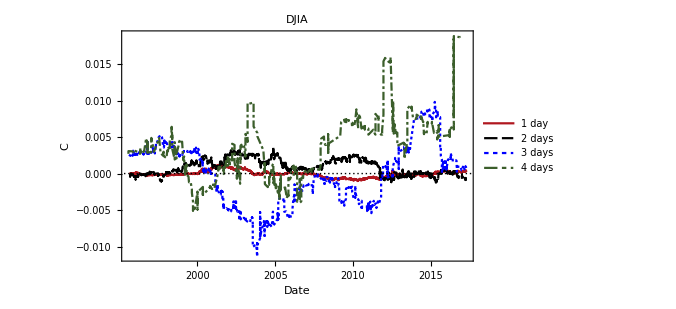
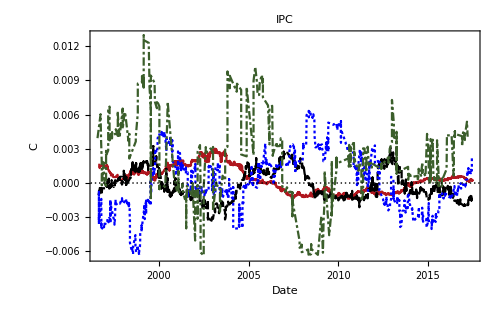
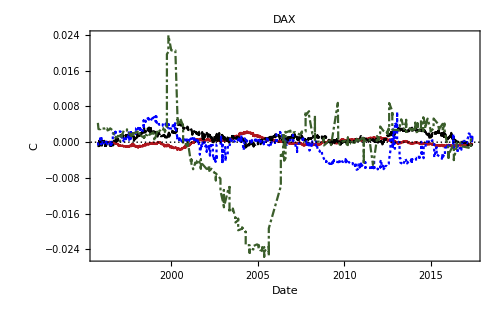
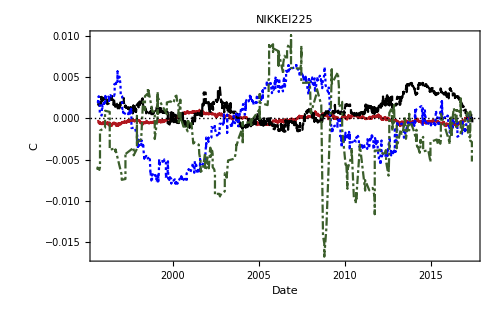

```mathematica
ProgressMap[RunCInTime[#,504]&,orderedDatabase]
```

Weak correlation

```mathematica
correlations = ProgressMap[RunCSignalCorrelation[#,504,Range[4],5]&,orderedDatabase];
```

```mathematica
Map[MatrixForm,correlations]
```

{(1. | 0.069244 | -0.101728 | -0.278023
0.069244 | 1. | -0.714902 | -0.347438
-0.101728 | -0.714902 | 1. | 0.167964
-0.278023 | -0.347438 | 0.167964 | 1.),(1. | -0.388162 | -0.377141 | 0.216665
-0.388162 | 1. | -0.0970296 | 0.203584
-0.377141 | -0.0970296 | 1. | -0.33365
0.216665 | 0.203584 | -0.33365 | 1.),(1. | -0.468797 | -0.331254 | -0.711009
-0.468797 | 1. | 0.207898 | 0.327137
-0.331254 | 0.207898 | 1. | 0.0141841
-0.711009 | 0.327137 | 0.0141841 | 1.),(1. | -0.343452 | -0.271681 | -0.250144
-0.343452 | 1. | -0.167395 | -0.400722
-0.271681 | -0.167395 | 1. | 0.280164
-0.250144 | -0.400722 | 0.280164 | 1.)}

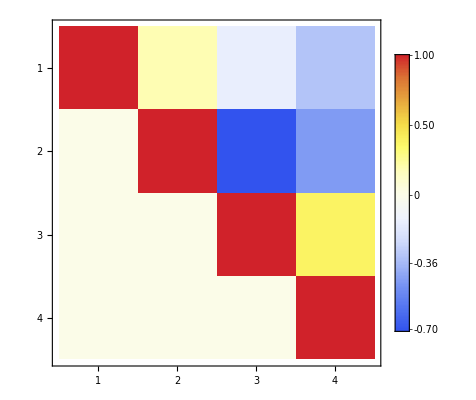
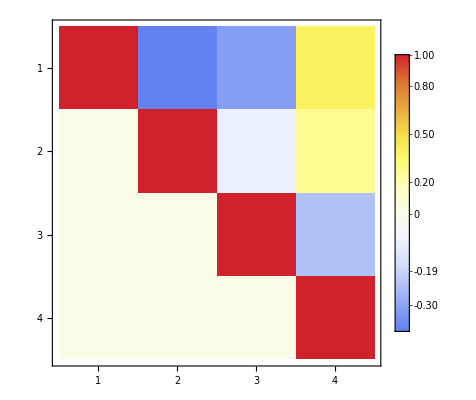
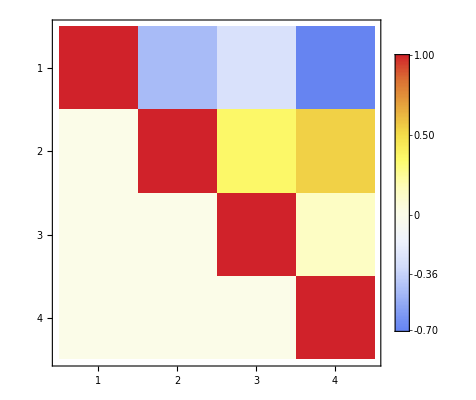
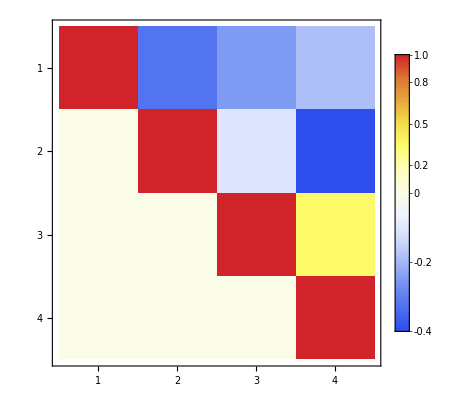

```mathematica
hideLower = UpperTriangularize[ConstantArray[1,{4,4}]];
Map[
MatrixPlot[
hideLower*#,
ColorFunction->"TemperatureMap",
PlotLegends->Automatic,
PlotRange->{All,All,{-1,1}}
]&,
correlations
]
```

Tn(0)

```mathematica
Tn0ByRun[runs_]:=Map[
{Last[#][[1]],MeasureTn[#[[All,2]],0.05,50]["Tn(0)"]}&,
runs
];

RunTn0InTime[market_,windowSize_,runs_:{1,2,3,4},skip_:1]:=Block[{runReturns,part,groupedInTime,symmInTime,objSize,pltData,upp},
runReturns = Thread[{TrendDuration[market["Prices"]],market["DatedTrendReturns"][[All,1]],market["TrendReturns"]}];
part = Partition[runReturns,windowSize,skip];
groupedInTime = Map[Part[GroupDatedReturnsByRun[#],runs]&,part];
symmInTime = Map[Tn0ByRun,groupedInTime];

objSize = Length[First[symmInTime]];
pltData = Table[symmInTime[[All,i]],{i,objSize}];

upp = Map[UpperPercentagePointLine[First[market["DatedTrendReturns"]][[1]],Last[market["DatedTrendReturns"]][[1]],#]&,{0.01,0.05,0.1}];
pltData = Append[pltData,UpperPercentagePointLine[First[pltData[[1]]][[1]],Last[pltData[[1]]][[1]],0.05]];

DateListPlot[
pltData,
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["Date",bigFontSize],Style["T_n(0)",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Append[DayLegends[runs],"95% CL"],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003],RGBColor[0.8200000000000001, 0.5, 0.]},
PlotMarkers->None,
PlotLabel->market["Name"],
GridLines->{dateObjects,{0}}
]
];
```

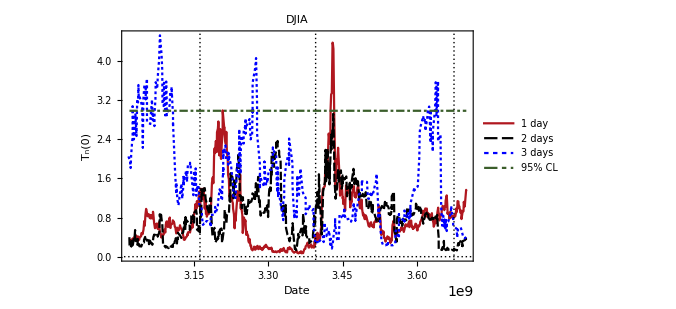
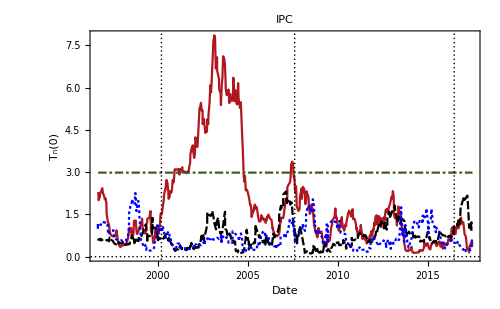
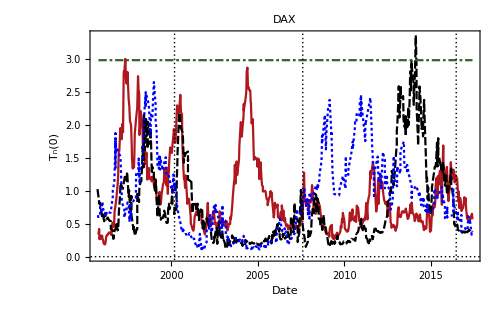
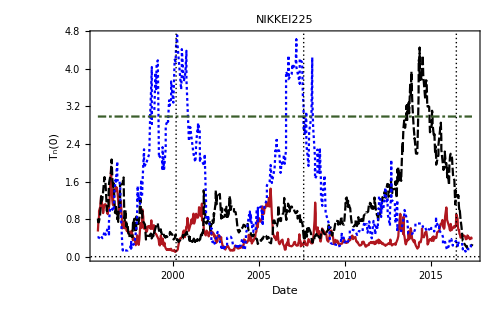

```mathematica
ProgressMap[RunTn0InTime[#,504,Range[3],5]&,orderedDatabase]
```

Waiting time

```mathematica
WaitTime[market_,duration_]:=Block[{td,grouped,dayIntervals},
td = TrendDuration[market["Prices"]];
grouped = Drop[Split[td,#≠duration&],1];
dayIntervals = Map[Length,grouped]-1;
Return[dayIntervals];
];
WaitTimeForMarket[market_]:=Block[{dist},
dist = Map[WaitTime[market,#]&,Range[4]];
SmoothHistogram[dist,1,
PlotRange->{{0,50},All},
PlotTheme->"Monochrome",
FrameLabel->{Style["Wait",bigFontSize],Style["PDF",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

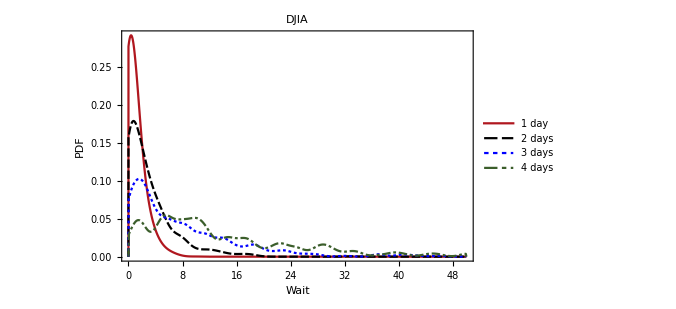
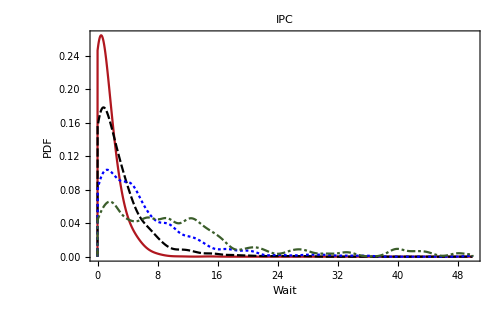
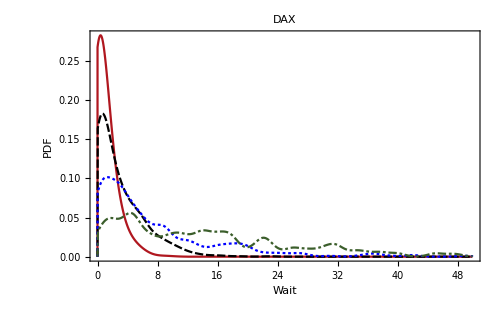
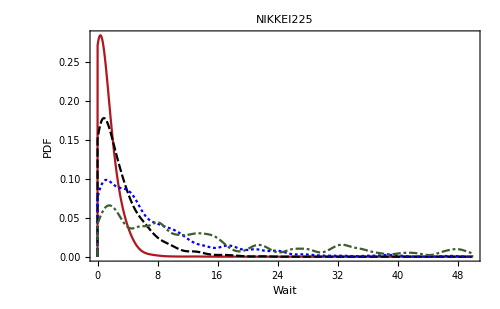

```mathematica
Map[WaitTimeForMarket,orderedDatabase]
```

Find fit automatically

```mathematica
FindWaitTimeDistributions[market_]:=Map[FindDistribution[WaitTime[market,#]]&,Range[4]];
FormatFindWaitTimeDist[market_]:=Labeled[Grid[Thread[{Range[4],FindWaitTimeDistributions[market]}]],market["Name"],Top];
Map[FormatFindWaitTimeDist,orderedDatabase]
```

{1 | GeometricDistribution[0.524653]
2 | GeometricDistribution[0.250443]
3 | GeometricDistribution[0.11392]
4 | GeometricDistribution[0.0619621]DJIA,1 | GeometricDistribution[0.451832]
2 | GeometricDistribution[0.251698]
3 | GeometricDistribution[0.140143]
4 | GeometricDistribution[0.0698213]IPC,1 | GeometricDistribution[0.5]
2 | GeometricDistribution[0.258578]
3 | GeometricDistribution[0.121295]
4 | GeometricDistribution[0.0601728]DAX,1 | GeometricDistribution[0.515115]
2 | GeometricDistribution[0.254356]
3 | GeometricDistribution[0.124503]
4 | GeometricDistribution[0.0573477]NIKKEI225}

Test for a geometric distribution

```mathematica
WaitTimeGOF[market_]:=Block[{dist,testData},
dist = Map[WaitTime[market,#]&,Range[4]];
testData = MapThread[{GeometricDistribution[#2],PearsonChiSquareTest[#1,GeometricDistribution[#2]]}&,{dist,{0.5,0.25,0.125,0.0625}}];

Labeled[
Grid[
Prepend[testData,{"Hypothesis","p-value"}],
Dividers->{{False,True},{False,True}}
],
market["Name"],
Top
]
];
```

```mathematica
Map[WaitTimeGOF,orderedDatabase]
```

{Hypothesis | p-value
GeometricDistribution[0.5] | 0.10662
GeometricDistribution[0.25] | 0.101582
GeometricDistribution[0.125] | 0.426596
GeometricDistribution[0.0625] | 0.0562684DJIA,Hypothesis | p-value
GeometricDistribution[0.5] | 1.13327×10^-6
GeometricDistribution[0.25] | 0.47862
GeometricDistribution[0.125] | 0.0373035
GeometricDistribution[0.0625] | 0.0453177IPC,Hypothesis | p-value
GeometricDistribution[0.5] | 0.871465
GeometricDistribution[0.25] | 0.137715
GeometricDistribution[0.125] | 0.395779
GeometricDistribution[0.0625] | 0.259944DAX,Hypothesis | p-value
GeometricDistribution[0.5] | 0.0929508
GeometricDistribution[0.25] | 0.950955
GeometricDistribution[0.125] | 0.857321
GeometricDistribution[0.0625] | 0.482176NIKKEI225}

## Stylized facts on run distributions

Correlation

```mathematica
PlotRunCorrelation[market_]:=Block[{grouped,corr},
grouped = Extract[GroupReturnsByRun[market,"TrendReturns"],Transpose[{{1,2,3,4}}]];
corr = Map[CorrelationFunction[#,{30}]&,grouped];

ListLinePlot[
corr,
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Correlation",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

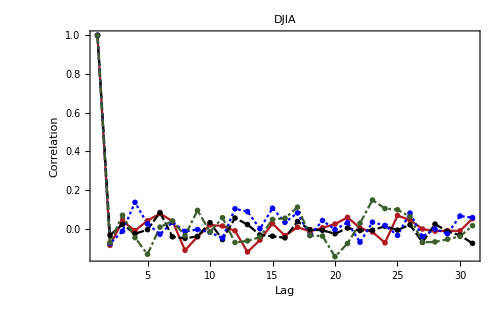
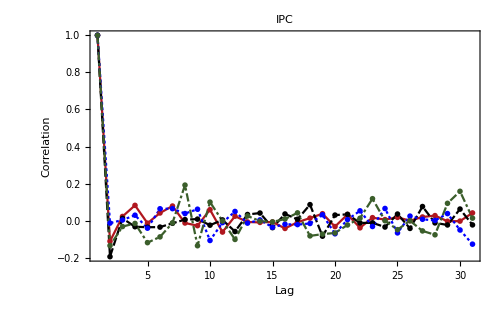
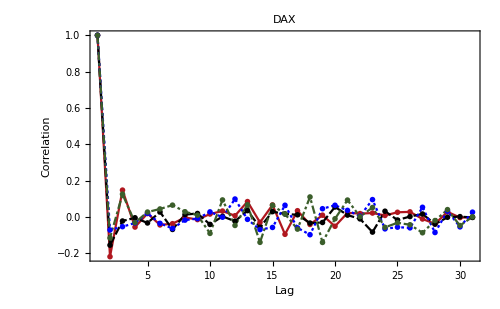
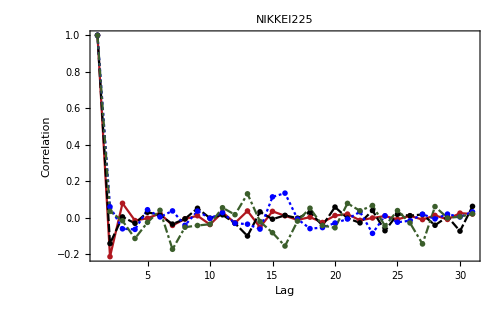

```mathematica
Map[PlotRunCorrelation,orderedDatabase]
```

Volatility (correlation of squared returns)

```mathematica
PlotRunVolatility[market_]:=Block[{grouped,volatilityClustering},
grouped = Extract[GroupReturnsByRun[market,"TrendReturns"],Transpose[{{1,2,3,4}}]];
volatilityClustering = Map[CorrelationFunction[#^2,{30}]&,grouped];

ListLinePlot[
volatilityClustering,
PlotRange->All,
PlotTheme->"Monochrome",
FrameLabel->{Style["Lag",bigFontSize],Style["Correlation",bigFontSize]},
PlotLegends->If[market["Name"]=="DJIA",Placed[DayLegends[4],{Right,Top}],None],
ImageSize->plotSize,
Frame->True,
BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.230003, 0.370006, 0.170003]},
PlotLabel->market["Name"]
]
];
```

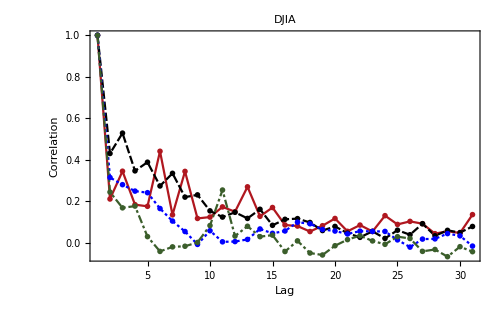
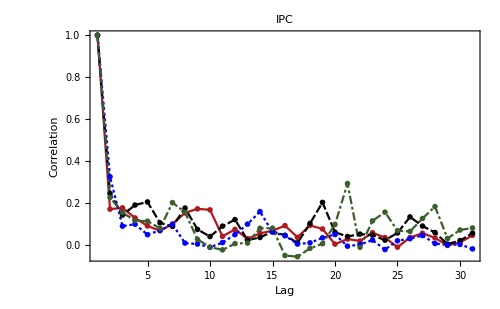
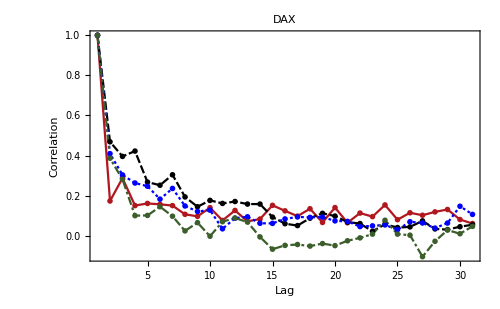
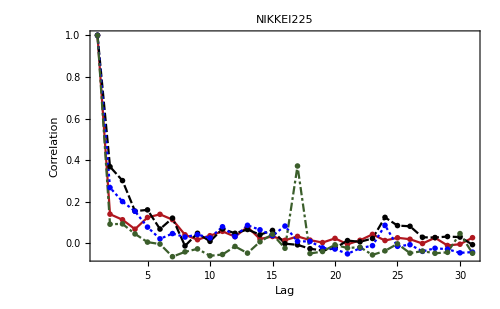

```mathematica
Map[PlotRunVolatility,orderedDatabase]
```

## Symmetry analysis

```mathematica
UpperPercentagePointLine[cmin_,cmax_,cl_]:= {{cmin, UpperPercentagePoint[cl]},{cmax,UpperPercentagePoint[cl]}};

PlotSymmetry[market_,returnType_]:= Module[{returns,standardError,tn,upperLineLimit,meanline,cMax,cMin,cFill,cline,upp,plotData,p},
returns = market[returnType];
standardError = StandardDeviation[returns] / Sqrt[Length[returns]];
tn = MeasureTn[returns];
upperLineLimit = Max[tn["TnValues"][[All,2]]];

(* Plot lines *)
meanline=Line[{{Mean[returns],0},{Mean[returns],upperLineLimit/2.5}}];

cMin = Line[{{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMin"],upperLineLimit/2.5}}];
cMax = Line[{{tn["PlausibleSymmMax"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}}];
cFill = Rectangle[{tn["PlausibleSymmMin"],0},{tn["PlausibleSymmMax"],upperLineLimit/2.5}];

cline = Line[{{MinimalBy[tn["TnValues"],Last][[1,1]],0},{MinimalBy[tn["TnValues"],Last][[1,1]],upperLineLimit/2.5}}];
upp = Map[UpperPercentagePointLine[tn["MinimumC"],tn["MaximumC"],#]&,{0.01,0.05,0.1}];
plotData = Join[{tn["TnValues"]},upp];

p = ListLinePlot[plotData,
PlotTheme->"Monochrome",
FrameLabel->{
Style["c",bigFontSize],
Style["T_n(c)",bigFontSize]
},
Epilog->{
meanline,
cline,
cMin,
cMax,

{
Gray,
Opacity[0.4],
cFill
},

Inset[Text["μ"],{Mean[returns],upperLineLimit/2}],
Inset[Text["C_Max"],{tn["PlausibleSymmMax"],upperLineLimit/2}],
Inset[Text["C_Min"],{tn["PlausibleSymmMin"],upperLineLimit/2}],
Inset[Text["C"],{MinimalBy[tn["TnValues"],Last][[1,1]],1.7+upperLineLimit/2}]
},
PlotLegends->If[market["Name"]=="DJIA",Placed[{"T_n","99% CL","95% CL","90% CL"},{Right,Top}],None], 
PlotLabel->market["Name"],ImageSize->plotSize,Frame->True,BaseStyle->FontSize->smallFontSize,
TicksStyle->Large,PlotMarkers->None, PlotStyle->colors
];
Return[p];
];
```

Returns

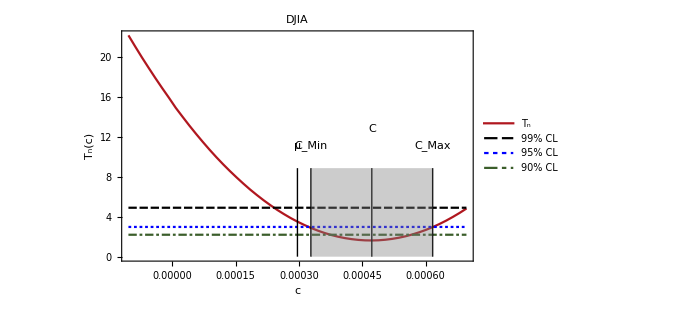
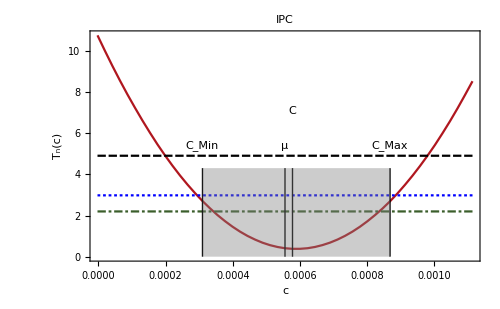
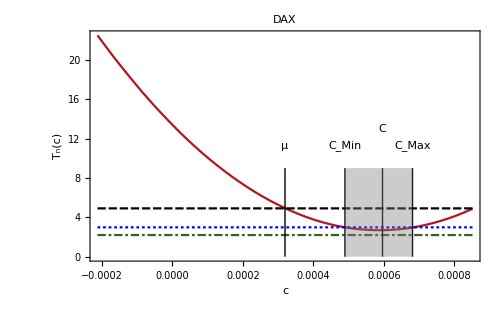
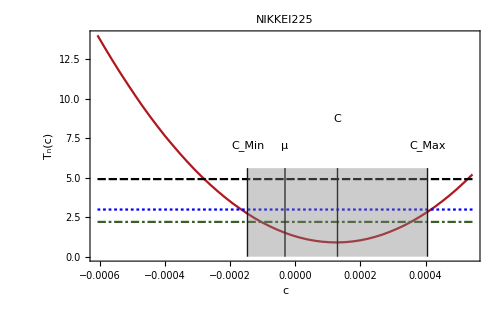

```mathematica
ProgressMap[PlotSymmetry[#,"Returns"]&,orderedDatabase]
```

Trend returns

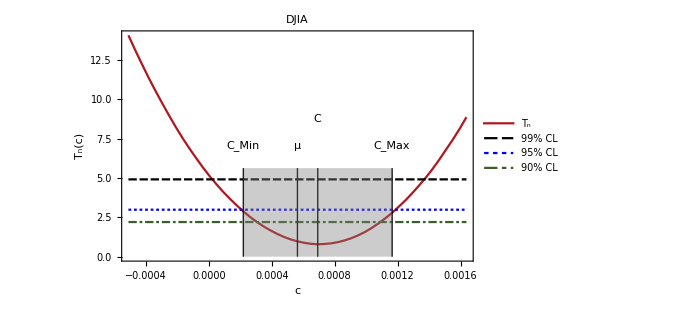
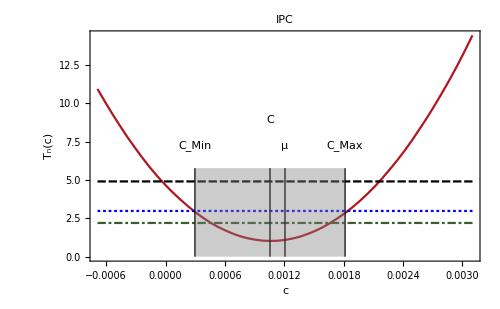
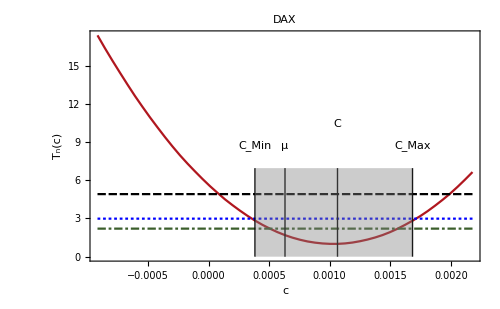
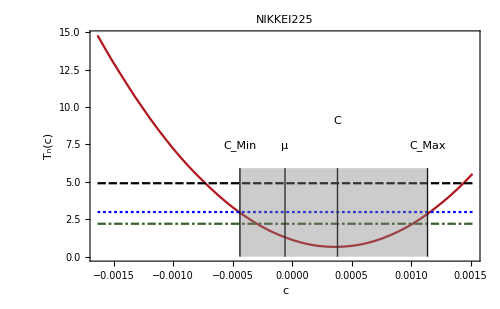

```mathematica
Map[PlotSymmetry[#,"TrendReturns"]&,orderedDatabase]
```

Velocity trend returns

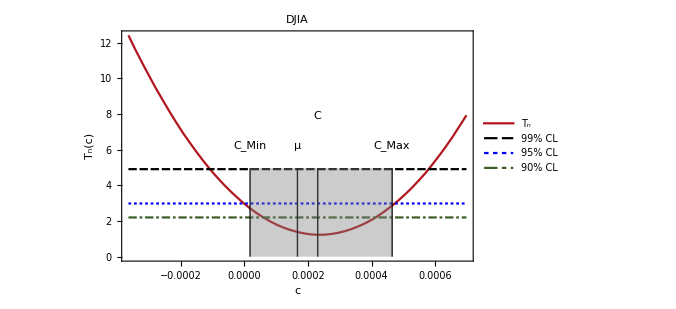
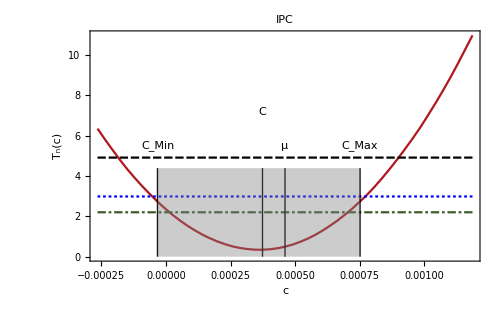
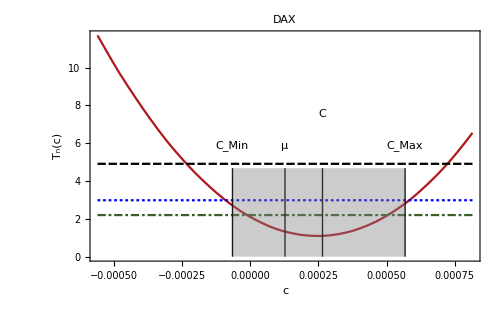
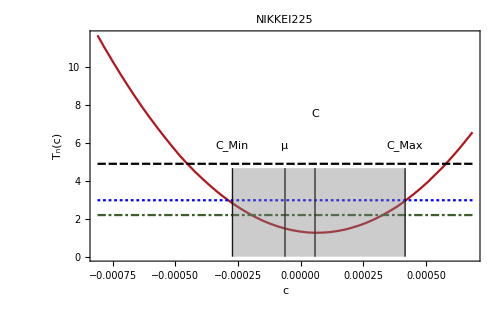

```mathematica
Map[PlotSymmetry[#,"VelocityTrendReturns"]&,orderedDatabase]
```

## Symmetry tables of the test when c=0

```mathematica
ReportSymmetry[market_,returnType_,cl_]:= Block[{data, returns},
returns =  market[returnType];
If[Tn[N[returns],0.0] ≤ UpperPercentagePoint[cl],
Return[Item["Symmetric",Background->RGBColor[0.2,1,0.2]]],
Return[Item["Asymmetric",Background->RGBColor[1,0.2,0.2]]]
];
];
MarketSymmetryReport[market_,cl_]:= Join[
{market["Name"]},
Table[ReportSymmetry[market,returnType,cl],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]
];
MakeSymmetryTable[database_,cl_]:=Block[{symmTable,grid},
symmTable = Table[MarketSymmetryReport[market,cl],{market,database}];

grid = Grid[
Join[
{
{"CL = "<>ToString[cl],SpanFromLeft,SpanFromLeft},
{Style["Market",Bold],Style["R",Bold],Style["R_T",Bold],Style["VR_T",Bold]}
}
,
symmTable
]
,
Frame->All,
Background->{{LightGray},{Gray}}
];
Return[grid];
];
```

```mathematica
Table[MakeSymmetryTable[database,cl],{cl,{0.01,0.05,0.1}}]
```

{CL = 0.01 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Symmetric
IPC | Asymmetric | Symmetric | Symmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric,CL = 0.05 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Symmetric
IPC | Asymmetric | Asymmetric | Symmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric,CL = 0.1 |  |  | 
Market | R | R_T | VR_T
DAX | Asymmetric | Asymmetric | Symmetric
DJIA | Asymmetric | Asymmetric | Asymmetric
IPC | Asymmetric | Asymmetric | Asymmetric
NIKKEI225 | Symmetric | Symmetric | Symmetric}

```mathematica
MarketRowTn[market_,returnType_]:=Block[{tn},
tn = MeasureTn[market[returnType],0.05,350];
{
market["Name"],
returnType,
ToString[tn["Mean"]],StringJoin["(",TextString[tn["PlausibleSymmMin"]],", ",ToString[tn["PlausibleSymmMax"]],")"],
ToString[tn["BestSymmetry"]],
If[tn["Tn(0)"]<UpperPercentagePoint[0.05],"Yes","No"]
}
];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
marketTables = ProgressMap[Table[MarketRowTn[#,returnType],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]&,orderedDatabase];
```

```mathematica
Grid[
Join[{{"Market","Observable","μ","Symmetry Interval","C","Zero Symmetric"}},Concatenate[marketTables]],
Background->{None,{LightBlue}},
Frame->All
]
```

Market | Observable | μ | Symmetry Interval | C | Zero Symmetric
DJIA | Returns | 0.000296114 | (0.000323572, 0.000616454) | 0.000470013 | No
DJIA | TrendReturns | 0.000563473 | (0.000207432, 0.00118348) | 0.000692385 | No
DJIA | VelocityTrendReturns | 0.000166781 | (-0.000000150935, 0.000470294) | 0.000230519 | Yes
IPC | Returns | 0.000555369 | (0.000294031, 0.000883634) | 0.000590426 | No
IPC | TrendReturns | 0.00120697 | (0.000286817, 0.00183484) | 0.00107707 | No
IPC | VelocityTrendReturns | 0.00046062 | (-0.0000531519, 0.000767226) | 0.00036118 | Yes
DAX | Returns | 0.000319714 | (0.000489751, 0.000681043) | 0.000589952 | No
DAX | TrendReturns | 0.000631323 | (0.000365994, 0.00171033) | 0.00103816 | No
DAX | VelocityTrendReturns | 0.000127415 | (-0.0000888628, 0.000583565) | 0.000249317 | Yes
NIKKEI225 | Returns | -0.0000312847 | (-0.000162716, 0.000415581) | 0.000129718 | Yes
NIKKEI225 | TrendReturns | -0.000059991 | (-0.000437956, 0.0011549) | 0.00036297 | Yes
NIKKEI225 | VelocityTrendReturns | -0.0000621582 | (-0.000284413, 0.000416544) | 0.0000617915 | Yes

## Descriptive statistics

```mathematica
MarketRowStat[market_,returnType_]:=Block[{rets},
rets = market[returnType];

{
market["Name"],
returnType,
ToString[Length[rets]],
ToString[Count[rets,_?Positive]],
ToString[Count[rets,_?Negative]],
ToString[Count[rets,x_/;x==0]],
ToString[Mean[rets]],
ToString[StandardDeviation[rets]],
ToString[Skewness[rets]],
ToString[Kurtosis[rets]]
}
];
```

```mathematica
orderedDatabase = {database[[2]],database[[3]],database[[1]],database[[4]]};
```

```mathematica
marketTables = Map[Table[MarketRowStat[#,returnType],{returnType,{"Returns","TrendReturns","VelocityTrendReturns"}}]&,orderedDatabase];
```

```mathematica
Grid[
Join[{{"Market","Observable","Entries","Positive Events", "Negative events","Zero events","μ","σ","Skewness","Kurtosis"}},Concatenate[marketTables]],
Background->{None,{LightBlue}},
Frame->All
]
```

Market | Observable | Entries | Positive Events | Negative events | Zero events | μ | σ | Skewness | Kurtosis
DJIA | Returns | 6447 | 3391 | 3012 | 44 | 0.000296114 | 0.0107171 | -0.176113 | 11.569
DJIA | TrendReturns | 3388 | 1677 | 1670 | 41 | 0.000563473 | 0.0208431 | -0.693697 | 14.9535
DJIA | VelocityTrendReturns | 3388 | 1677 | 1670 | 41 | 0.000166781 | 0.0103054 | 0.378788 | 13.9691
IPC | Returns | 6409 | 3362 | 3041 | 6 | 0.000555369 | 0.0148833 | 0.0226418 | 9.35525
IPC | TrendReturns | 2949 | 1472 | 1471 | 6 | 0.00120697 | 0.0342922 | -0.241625 | 9.67833
IPC | VelocityTrendReturns | 2949 | 1472 | 1471 | 6 | 0.00046062 | 0.0131251 | 0.152915 | 5.84517
DAX | Returns | 6465 | 3457 | 3004 | 4 | 0.000319714 | 0.0142415 | -0.106661 | 7.30022
DAX | TrendReturns | 3274 | 1634 | 1636 | 4 | 0.000631323 | 0.0295203 | -0.729049 | 10.8335
DAX | VelocityTrendReturns | 3274 | 1634 | 1636 | 4 | 0.000127415 | 0.0131252 | -0.0275892 | 5.43131
NIKKEI225 | Returns | 6282 | 3183 | 3094 | 5 | -0.0000312847 | 0.0151916 | -0.203261 | 8.09446
NIKKEI225 | TrendReturns | 3276 | 1636 | 1635 | 5 | -0.000059991 | 0.0300463 | -0.569394 | 11.9555
NIKKEI225 | VelocityTrendReturns | 3276 | 1636 | 1635 | 5 | -0.0000621582 | 0.0142704 | -0.257632 | 6.8131

## Trend duration table

```mathematica
TDRowStat[market_]:=Block[{duration,trendLength,events},
duration = TrendDuration[market["Prices"]];
trendLength = Sort[DeleteDuplicates[duration]];
events = Map[Count[duration,#]&,Range[13]];
Join[{market["Name"]},events]
];

TDRowStatSigned[market_,signf_]:=Block[{duration,trendLength,events},
duration = Select[Thread[{TrendDuration[market["Prices"]],TrendReturns[market["Prices"]]}],signf[Last[#]]&][[All,1]];
trendLength = Sort[DeleteDuplicates[duration]];
events = Map[Count[duration,#]&,Range[13]];
Join[{market["Name"]},events]
];
```

```mathematica
m = Map[TDRowStatSigned[#,Positive]&,orderedDatabase]
```

{{DJIA,824,425,200,129,46,25,16,6,2,2,1,1,0},{IPC,629,372,204,119,67,40,18,12,6,5,0,0,0},{DAX,754,436,200,114,72,30,13,7,2,1,1,3,1},{NIKKEI225,821,429,211,89,41,23,12,5,4,0,0,1,0}}

```mathematica
Grid[
Join[{{"Market","1","2","3","4","5","6","7","8","9","10","11","12","13"}},Map[TDRowStat,orderedDatabase]],
Background->{None,{LightBlue}},
Frame->All
]
```

Market | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
DJIA | 1778 | 848 | 383 | 214 | 86 | 43 | 21 | 9 | 2 | 2 | 1 | 1 | 0
IPC | 1333 | 741 | 413 | 209 | 123 | 64 | 32 | 16 | 12 | 6 | 0 | 0 | 0
DAX | 1637 | 844 | 397 | 200 | 112 | 45 | 21 | 8 | 3 | 1 | 2 | 3 | 1
NIKKEI225 | 1688 | 832 | 407 | 190 | 80 | 38 | 23 | 8 | 8 | 0 | 0 | 2 | 0